# Submissions to the 2011 Mathematica One-Liner Competition

Variable names used in some submissions may clash. If an entry doesn’t appear to work, try restarting the kernel to clear all variable definitions and evaluating again.

## 1 Random cluster generator

#### Jeremy Vates

The program is a random cluster generator, each execution produces a different result. Enjoy

```mathematica
n := RandomInteger[99];
P:= {n,n,n};
R:= {n,n,n};
S := {n,n,n};
T := {n,n,n};
Q = {};
For [ i = 0, i<n, i++, AppendTo[Q, {P->R,R->S,S->P,S->T,T->P}]];
GraphPlot3D[Q]
```

## 2 Stock market volatility

#### Bob Rimmer

While it may seem obvious, it works in CDF Player when Script.m has been created with the function Encode.  Script.m may be an encoded Mathematica package or a simple script created by saving a Mathematica notebook containing initialization cells as a .m file.  It offers a way to use protected content with CDF Player.

(Clarification from the submitter after I objected to some of his code being in packages:)

The point of it was not to load the package but to let people know it could be done.  Perhaps the line is bug in Mathematica, but it is a useful one in that it allows people to create SECURE CDFs, something which is not advertised.

The following output shows recent stock market volatility as measured by the daily Log[High/Low] of the SP500 index.

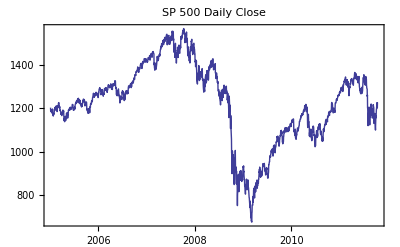

Latest data: Tue 18 Oct 2011

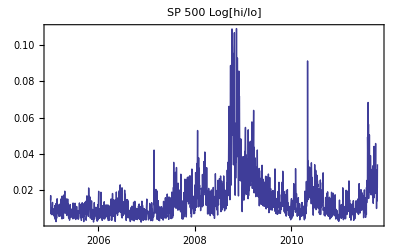

Recent values: {0.0293883,0.0310414,0.0249569,0.035814,0.045783,0.0268746,0.0266045,0.0182116,0.031247,0.0100062,0.0199142,0.0140784,0.0156036,0.0213956,0.0343351}

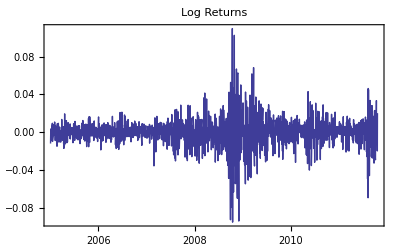

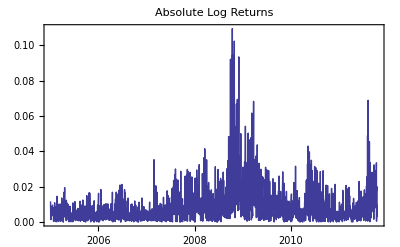

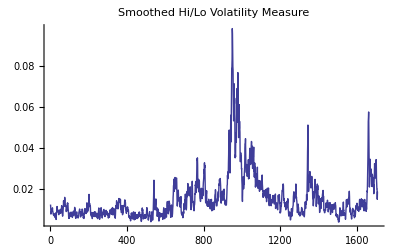

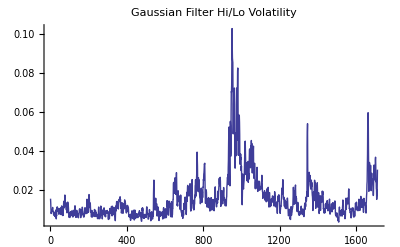

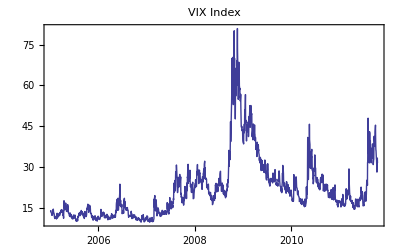

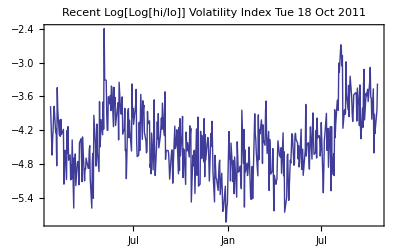

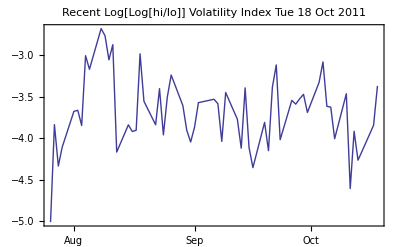

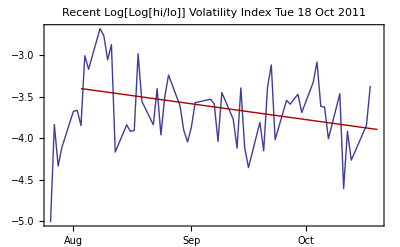

Projected current volatility from trend: 0.0203465

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Script.m"}]];
```

## 3 Cryptography

#### Bob Rimmer

The one - liner below puts out a stream of cryptographically secure random bytes.  Because the key is small relative to the modulus the first few bytes are a little less secure than the rest, in a real world cryptographic situation you would probalby be happy to use a little longer code than 140 characters, by lengthening the key, the first value of x in the code.

```mathematica
x=9274567890123987234567315;B=(p=1;While[Mod[p,4]<3,p=RandomPrime[{2^(#),2^(#+1)}]];p)&;
l=2^12;m=B[l]*B[l];Table[Mod[x=Mod[x^2,m],256],{l}]
```

To see how it works save the bytes.

```mathematica
code=%;
```

Here is the modulus.

```mathematica
m
Log[2.,m]
```

8193.3

As long as p remains on the system one can factor the modulus, so it is critical for user not to leave Mathematica running..

```mathematica
m/p
m==% p
```

Encrypt a text message

```mathematica
text=StringTake[ExampleData[{"Text","DeclarationOfIndependence"}],4096]
```

```mathematica
message=FromCharacterCode[BitXor[ToCharacterCode[text],code]]
```

```mathematica
ListPlot[ToCharacterCode[message]]
```

```mathematica
modulus=FromCharacterCode[IntegerDigits[m,256]]
```

Recover the message with the key and the modulus.

```mathematica
x=9274567890123987234567315;
FromCharacterCode[BitXor[ToCharacterCode[message],Table[Mod[x=PowerMod[x,2,FromDigits[ToCharacterCode[modulus],256]],256],{4096}]]]
```

## 4 Cell nucleus(?) detection

#### Ronald T. Kurnik

```mathematica
a=-Graphics-;
ImageMultiply[ColorNegate[EdgeDetect[Opening[ChanVeseBinarize[a],DiskMatrix[6]]]],a]
```

## 5 White Space Data

#### Zdenek Buk

The following code generates the black and white portrait of Stephen Wolfram. The code has exactly 125 character (counted by One-Liner counter tool). The result image has resolution 57x89 pixels.
The code demonstrates the flexibility of the powerful Mathematica language and the notebook (CDF) format — all the image data are encoded using white space characters “ “ and “\t” (space and tab), which does not count.

```mathematica
SelectionMove[n=InputNotebook[],All,EvaluationCell];Image[Partition[Characters[NotebookRead[n]⟦1,1,1,-1⟧]/.{" "->0,"\t"->1},57]]
```

## 6 Psycho Pie Chart

#### Susan B. Garavaglia

```mathematica
Animate[j="ColorList";PieChart[Mod[Table[x,{x,Length[ColorData[z,j]]}],3,1],ChartStyle-> ColorData[z,j],SectorSpacing-> {z/124,0}],{z,1,62,1}]
```

## 7 Recursive Image Collage

#### Zdenek Buk

This code creates recursive image collage. It takes the image from example data, resize it to some reasonable size (in the code 50 pixel - the oragne parameter). Each pixel is then replaced by the lighter or darker image image itself and assembled together.

```mathematica
ImageAssemble[Round[Rescale[ImageData[i=Nest[Darker,ImageResize[ExampleData[{"TestImage","Elaine"}],50],3]]]9]/.n_Integer:>Nest[Lighter,i,n]]
```

## 8 The music of π

#### Chuck Ronco

This code plays a piece of music which is made by assigning a musical note to the first 51 digits of π.

```mathematica
Sound[SoundNote@@@Table[{{RealDigits[N[Pi,51]][[1,i]]},.46,"NewAge"},{i,51}]/.ArrayRules[ToString/@{C,D,E,F5,G,A1,B3,C5,D5,C3}]]
```

## 9 Hollow Borg Maker

#### Alex Hirsbrunner

```mathematica
ρ:=Random[];
r=RotateLeft;
Graphics3D[Table[{RGBColor[.2,ρ,.2],Cuboid[λ=r[{ζ,ρ,ρ},α],λ+r[ρ/8{Sign[ζ-.5],ρ,ρ},α]]},{ζ,{0,1}},{α,0,2},{6!}]]
```

## 10 Gödel Encoding

#### Seth Chandler

This code shows Godel encoding and decoding and provides an example all in 140 characters

Submitted by 31852998818558033335583569518553969713562979256128852413435028584802280095132522915140852059213615885254195383571392329794922795770707713352146132246733450817203684706031624389326814445278593644015851830555147332529972730476371111032928755121669696320885322183371137549132678432325201321088291961932580795793316150460426896515876907565150898560632356597516757851357415611268306151448502575725038303109117520756585040637353884083814809618027876589084800550085669844190330414147732550776588969619513322100360836563670259998808000105843033565683125271219305040872492121918200700876096236568371415108885971202966692731542755155492545496777273761370133487468567897462061467988376352832702315263386208621024682610032132167221326665443603070121933843787714625473074088393813087118335189447111448481209324764626872396537657918153867513626139799252903903579497300408157148993212503430708639120637878373602264372520192507118407030815100401660701892350808564985612891426172887004090304961010597754862098963868563937675567960224206117165314984013984751736456325794242971808220809539526648631141733630175443888198290657013932712581042593347398080341176139063840921955225351081940691333166585332495476849218163059490261568862612446747917691336537354355583988294420055872348436734477472820888912652549574502842376763480900293536270489869173917909554005870573478047831251930361273134466324993052381742040775103238037710739217725809705890890199297359324363890136345102176332563773052736934355799964704578145781579839114854178134957587706285155730771781779074683120290636180494633473596772222439807794084877433524743508121536977243542428903615785509096364128559822603957502309550068089204170004870341999259903069461437157089594917862703258076788062919696008096731130489899333544526637777423836834689699257813758834664664702722431746838186880481843974083785730479285180650715536825291216951978395107163555995600897312089089922492665080729237560882624123527445384971557683045206839860774047216674299958416859907636891339706469490540321709968679566095063058180847277195299703620721527637052382117246306439136726343437118872830156537112158640537600000000000000000000000000000000

```mathematica
𝒢[s_]:=Reap[FromCharacterCode[Last/@FactorInteger@Sow[Times@@(Prime[Range@Length@#]^#)]&@ToCharacterCode@s]];𝒢["Godel encoding makes big numbers"]
```

## 11 Random shuffling

#### Antonin Slavik

```mathematica
l=Flatten@ImagePartition[ExampleData@{"TestImage","Lena"},64];Dynamic[{t,f}=RandomSample[l,2];ImageAssemble@Partition[l=l/.{t->f,f->t},8]]
```

## 12 Spyglass

#### Antonin Slavik

```mathematica
i=ExampleData@{"TestImage","Lena"};m=DiskMatrix[80,2^9]+.2;Dynamic@ImageMultiply[i,Image[m=RotateRight[m,RandomInteger[{-30,30},{2}]]]]
```

## 13 Down the drain

#### Yves Klett

If this does not make it, then do away with the smiling face!

```mathematica
Manipulate[r=1/(u^2+v^2+o);ParametricPlot3D[RotationMatrix[r,{0,0,1}].{u,v,-r},{u,-1,1},{v,-1,1},PlotStyle->Texture[Style[☺,10^3]]],{o,9,.1}]
```

## 14 Instant Recursive Art

#### Yves Klett

Is your code beautyful? See for yourself and paste this line into your favorite notebook or help page and evaluate. Evaluate multiple times for enhanced effect. Be prepared to ugrade your machine. Make your local artist envious. Test your skills to the max by reverse engineering the code. Write code that looks like a bumblebee!

```mathematica
Colorize@WatershedComponents[Erosion[ImportString[ExportString[EvaluationNotebook[],"JPG"],"JPG"],1]]
```

## 15 Spherical

#### Radko Kriz

```mathematica
Animate[SphericalPlot3D[a+Sin[3ϕ] Sin[20θ]/9,{θ,0,π},{ϕ,0,2π},ColorFunction->"Rainbow",Mesh->None,PlotPoints->50,Axes->False],
{a,0.5,0.1}]
```

## 16 Revolution

#### Radko Kriz

```mathematica
ListAnimate[ParallelTable[RevolutionPlot3D[t^(2a)-t^2,{t,-1,1},RevolutionAxis->{1,1,0},Boxed->False,Axes->False],{a,1,10}]]
```

## 17 Echidnahedron

#### Radko Kriz

```mathematica
Animate[Graphics3D[{Opacity[a],Glow[RGBColor[a,1-a,1-a]],EdgeForm[White],Lighting->None,PolyhedronData["Echidnahedron","Faces"]}],{a,0,1}
]
```

## 18 Desktop Search Engine

#### Sascha Kratky

The following one-liner is a helper function that is handy in daily use. It acts as a replacement for desktop search engines like Spotlight or Google Desktop Search and lets you search the contents of files using a Manipulate.

```mathematica
DS[d_,f_]:=Manipulate[
Pick[x⟦1⟧,Or@@StringMatchQ[#,ToString[s]]&/@x⟦2⟧],
{s},
Initialization:>{x=FileNames[f,d,∞]//{#,ReadList[#,Word]&/@#}&}
]
```

In the Manipulate text box you can use wildcard characters supported by StringMatchQ.

Example Use (then enter search string TODO):

```mathematica
DS[$InstallationDirectory,"*.m"]
```

One drawback of the function: If the computer’s hard drive is slow the Manipulate initialization may time out.

## 19 Collatz sequences

#### Craig Rollins

WRI one-liner judges,

The attached program computes Collatz sequences, and displays them on a semi-Log plot.

According to M.S. Word, the text file containing the program comes to 139 characters.

If for some reason, my count is off, the .nb file saved a couple of characters for the expressions 2^15 and 2^30, and I would like the benefit of the shorter character count.

It is an open question whether these sequences will always hit bottom. The plot suggests some sequences that haven’t hit bottom (YET). Will they eventually? The answer is available by adding PlotRange->All to the plot command, but as that brings me to more than 140 characters, I will need to leave you in suspense about that, emphasizing the open question at hand.

I had a lot of trouble trying to save the .nb file with the graphic contained within. It is omitted from the .nb file. Sorry. The competition rules don’t say that it is required.

Enjoy ! !

```mathematica
(* Added by Carlson *) ClearAll[f,p,i]
```

```mathematica
f[x_?EvenQ]:=x/2;

f[x_?OddQ]:=(3x+1)/2;

p={};i=0;

While[i<2^10,AppendTo[p,Log[2,NestWhileList[f,2^30+i,#>1&]//N]];
i++]

ListPlot[p,Joined->True]
```

## 20 Animated Sky Chart

#### Zdenek Buk

The following code shows the animated shy chart for the next ten days (in current time) — 10 has been chosen for the speed purposes. You can change it to any value.

```mathematica
g={#,WolframAlpha["sky chart "<>#,{{"SkyMap:AstronomicalData",1},"Content"}]}&/@(DateString[DatePlus[Date[],#]]&/@Range[10]);
ListAnimate[g]
```

## 21 Let the others do all the work

#### Yves Klett

Get a quick preview of the awesome featured demonstrations and click on them. Kudos to all demo authors and CDF plugin. The 140 character limit cut it somewhat sharp here.

```mathematica
i=Import
Hyperlink[i[#<>"HTMLImages/index.en/thumbnail_1.gif"],#]&/@i["http://demonstrations.wolfram.com/featured.html","Hyperlinks"]⟦7;;-14⟧
```

Import

## 22 Entry 1: All Nonisomorphic Graphs on Five or Fewer Vertices

#### Richard Mercer

This was motivated by a discussion with a student taking a course in Graph Theory who was assigned to list these graphs by hand. I wanted to show her that Mathematica could do this. It didn’t turn out like I hoped because I tried to use the option Method-> “CircularEmbedding”, but those graphs which used less than five vertices used different embeddings. This implementation gets around that problem.

```mathematica
F = GraphData;
r = Range[5];
v ={Cos[#],Sin[#]}&/@ (2π/5r);
g=Graph[r,#,VertexCoordinates->v]& /@ (F[#,"EdgeIndices"]& /@ F[5]);
Animate[g[[k]],{k,1,34,1}]
```

## 23 Wolf’s Tour

#### Richard Mercer

I attempted to create a “Knight’s Tour” demostration in 140 characters. This was frustrating because the implementations of the various commands required all conspired to make the code far longer than it really needed to be.

“KnightTourGraph” produced a graph with vertices indexed by numbers from 1 to 64 instead of grid coordinates. It required  28 characters to convert to grid coordinates.

“FindHamiltonianCycle” was the longest command name possible (in Wolfram tradition). It could have been “HamiltonianCycle” as it was in the Combinatorica package, or something shorter. Cost: 4+ characters.

The output of FindHamiltonianCycle was wrapped in a completely redundant set of braces, requiring an extra application of First to get rid of them. Cost: 6 characters.

The Grid default is to show no dividers, so I had to explicitly request them. Cost: 12 characters.

As a result of all this nonsense my code ended up with 150 characters. I could have saved one more but it was pointless. This is the Unofficial Entry. I also offer an Official Entry with no dividers, where the Knight’s Tour takes place on an invisible chessboard (137 characters). I think you’ll agree it just isn’t the same.

Please Note: If you reexecute these commands, press the “Slower” button 12 times to get a more reasonable Animation Speed.

#### Unofficial Entry (150)

```mathematica
Animate[Grid[ReplacePart[Table[" ",{8},{8}],(#[k-1,8]+1)& /@{Quotient,Mod}-> 🐺],Dividers-> All],{k,First/@ First @ FindHamiltonianCycle[KnightTourGraph[8,8]]}]
```

#### Official Entry (137)

```mathematica
Animate[Grid[ReplacePart[Table[" ",{8},{8}],(#[k,8]+1)& /@{Quotient,Mod}-> 🐺]],{k,First/@ First @ FindHamiltonianCycle[KnightTourGraph[8,8]]-1}]
```

## 24 Anagram Bands

#### William Wu

Description

This is a method for generating all anagrams of the form [Adjective] [Noun]. Many of the resulting anagrams would be ideal names for music bands. Some gems include: 
	supersonic percussion, insatiable banalities, paternalistic antiparticles, oceanic cocaine, isometric eroticism, sloppy polyps, ruthless hustlers, cosmic comics, angriest ingrates 

To fit within the 140 character limit, I employ a stochastic random sampling approach which is slow to generate the bands, but it works. 

Footnote: For a faster listing of all the solutions though, you can use the following algorithm which finishes more quickly: 
	Select[Flatten[Tuples[#,2]&/@GatherBy[DictionaryLookup@"*",Sort@Characters@#&],1],MemberQ[Tuples[WordData[#]⟦All,2⟧&/@#],{"Adjective","Noun"}]&]
but this is 142 characters.

```mathematica
RandomSample[WordData[All,#]]&/@{"Adjective","Noun"};Do[If[a≠n&&Equal@@(Sort@Characters@#&/@{a,n}),Print[a<>" "<>n]],{a,w⟦1⟧},{n,w⟦2⟧}]
```

poetical copalite

reformist firestorm

snub buns

takeout outtake

octuple couplet

supple peplus

gelid glide

north thorn

redolent rondelet

brainy binary

monied domine

plain lapin

russet tusser

russet estrus

$Aborted

## 25 Life’s Work, Easily Replaced

#### William Wu

```mathematica
ToExpression@Uncompress@"1:eJxTTMoPCrZjYGDQCEgsLU51MLJWtrFTUtBVSEnNSS1JTdFT0tfXqA4oyswrcVDWCS5ITcx2UK5V09RU03dwy8xJ9UvMTS2OjgUAuVYUpg==";
```

## 26 I Could Lose My Job For This

#### William Wu

Description:

At a certain lab, the doors are secured by combination locks with five buttons, numbered 1,2,3,4,5. 
The passcodes for these combination locks all adhere to the following rules:

1. The passcode consists of exactly 1 two-button press, and two 1-button presses.
2. No number can be punched more than once.

The following Mathematica one-liner generates all 180 passcodes that adhere to these rules. 
Given that it takes 5 seconds to test out a combination, any door at this lab can be broken into in 7.5 minutes on average.
This has been verified in the field on many doors.

### Code:

```mathematica
Sort@Flatten[Table[Permutations[Append[#,pair]]&/@Subsets[Complement[Range@5,pair],{2}],{pair,Subsets[Range@5,{2}]}],2]
```

## 27 Generating Mazes

#### Dave Lawrence

This cellular automaton generates maze-like structures.
If a cell is a live and has 1-4 neighbors, it remains alive.
If a cell is dead and has exactly 3 neighbors, then it is born again.
Any other situation results in death.

```mathematica
ListAnimate[MatrixPlot/@CellularAutomaton[{744,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{RandomInteger[1,{9,9}],0},99]]
```

## 28 World’s Smallest Mathematica Quine

#### Dave Lawrence

[note from carlson: A quine is a computer program which takes no input and produces a copy of its own source code as its only output. The standard terms for these programs in the computability theory and computer science literature are self-replicating programs, self-reproducing programs, and self-copying programs.]

See below. Don’t miss it.

## 29 The Ulam Spiral

#### Dave Lawrence

The Ulam spiral is constructed by starting at (0,0) on the integer grid, spiraling outwards, and marking every time step that is prime.

```mathematica
s={Re@#,Im@#}&/@Fold[Join[#1,Last@#1+I^#2Range@#2/2]&,{0},Range@140];ListPlot[s,Joined->True,Epilog->{Point/@s⟦Prime@Range@PrimePi@Length@s⟧}]
```

## 30 Sierpinski carpet

#### Heather May

```mathematica
c[k_]:= Select[Range[3^k],Mod[#,3]==1&]
Graphics[Table[Outer[Rectangle[{#1,#2}/3^k,{#1 + 1,#2 + 1}/3^k]&,c[k],c[k]],{k,1,3}],Background->Red]
```

## 31 Fractal

#### Stephan Leibbrandt

```mathematica
Image@Compile[{},Block[{i,x,p},Table[i=0;x=0.I;p=r+I c;While[Abs@x≤√2&&i<9^3,x=x^2+p;++i];Tanh[(i/9^3)^(1/7)],{c,-1,1,.01},{r,-2,1,.01}]]][]
```

## 32 Shooter

#### Stephan Leibbrandt

Click to shoot before a disk is falling through.

```mathematica
X=Y=x=y=0
ClickPane[Dynamic@Graphics[{Point[{x,++y}],Disk@If[#.#>1&[{x,y}-{X,Y}],{X,Y-=.1},{X,Y}={RandomReal[9],9}]},PlotRange->9],({x,y}=#)&]
```

## 33 Slow Motion

#### Stephan Leibbrandt

The image shows “only” parts that are moving. Therefore, background is “not” shown. At least my iSight camera needed a certain light level. Move from left to right to observe the effect.

On my computer it took up to a minute before the image appeared. Then, speed was reasonable.  Calling CurrentImage[] before helps to reduce te startup time.

```mathematica
(p=Table[#[],{9}];
Dynamic[Fold[ImageDifference,#⟦1⟧,Rest@#]&[ImageSubtract@@@Partition[p=Join[Rest@p,{#[]}],2,1]]])&[CurrentImage]
```